# Analysing results from backward evolution

## JSON functions

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
ImportJSONData[files_]:=Module[{},
Switch[Head[files],
String,
Import[files,"RawJSON"],
List,
Import[#,"RawJSON"]&/@files
]
];
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

## Defining functions

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
angDevColumn=1;
geoDevColumn=2;
a1Column=3;
a2Column=4;
```

```mathematica
initialization[etaOrigin_, etaMin_, etaMax_,fName_:"/back_lap"]:=Module[{},
etaOriginal = etaOrigin;
folder="original_eta" <> ToString@etaOriginal;
etaOriginal = etaOriginal/10;
fileName=fName;

(*etaRange={0.4,0.6,0.7,0.8,0.9,1,1.2,1.3,1.4,1.5,1.6,1.7,2.3(*,2.7,2.8,2.9,3,3.1,3.3,3.4,3.6,3.7,3.9*)};
etaMin=0;
etaMax=Length@etaRange-1;*)

etaRange=Range[etaMin,etaMax];

backwardSimFilePaths = Table[folder<>fileName<>ToString[eta]<>".json",{eta, etaRange}];
backwardSimDataArray=ImportJSONData[backwardSimFilePaths];
etaRange =etaRange/10.;
]
```

### Geometric deviation

#### Importing data, some statistics and log scale

```mathematica
plotGeoDev[streamMin_,streamMax_, stepMin_, stepMax_]:=Module[{},
geoDev = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;stepMax]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];(*LOG SCALE*)
geoDevLog = Table[{etaRange[[i]], Log@Quantile[Abs@Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;stepMax]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];(*PLOTS*)
geoDevPlot=ListLinePlot[geoDev,PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Odchylenie geometryczne",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
geoDevLogPLot=ListLinePlot[geoDevLog, PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"|Odchylenie geometryczne| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Width of geometric deviation

```mathematica
plotGeoDevWidth:=Module[{},
geoDevWidth=geoDev[[2]];
geoDevWidth[[All,2]]=geoDev[[3,All,2]]-geoDev[[1,All,2]];
geoDevWidthPlot=ListLinePlot[{geoDevWidth}(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*),PlotRange->All,PlotLabel->"Szerokość odchylenia geometrycznego",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
(* Width of geometric deviation in logarithmic scale *)
geoDevWidthLog=geoDevWidth;
geoDevWidthLog[[All,2]]=Log@Abs@geoDevWidth[[All,2]];
geoDevWidthLogPlot=ListLinePlot[{geoDevWidthLog}(*,PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}]*),PlotRange->All,PlotLabel->"|Szerokość odchylenia geometrycznego| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Geometric deviation: final results

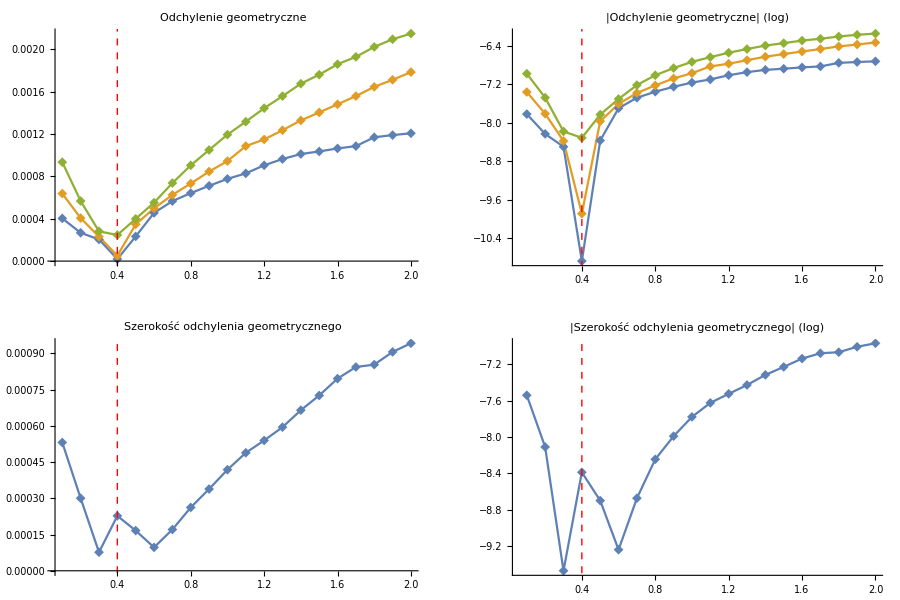

```mathematica
plotGeoDev[1,2,1,25]
plotGeoDevWidth
GraphicsGrid[{{geoDevPlot,geoDevLogPLot},{geoDevWidthPlot,geoDevWidthLogPlot}},Frame->All,ImageSize->900,AspectRatio->1/1.5]
```

### Angular deviation

#### Importing data, some statistics and log scale

```mathematica
plotAngDev[streamMin_,streamMax_, stepMin_, stepMax_]:=Module[{},
angDev = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, angDevColumn]][[All,stepMin;;stepMax]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];

(*LOG SCALE*)
angDevLog = Table[{etaRange[[i]], Log@Quantile[Abs@Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, angDevColumn]][[All,stepMin;;stepMax]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];(*/.{Indeterminate->-25};*)

(*PLOTS*)
angDevPlot=ListLinePlot[angDev,PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Odchylenie kątowe",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
angDevLogPLot=ListLinePlot[angDevLog, PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"|Odchylenie kątowe| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Width of angular deviation

```mathematica
plotAngDevWidth:=Module[{},
angDevWidth=angDev[[2]];
angDevWidth[[All,2]]=angDev[[3,All,2]]-angDev[[2,All,2]];
angDevWidthPlot=ListLinePlot[{angDevWidth}(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*),PlotRange->All,PlotLabel->"Szerokość odchylenia kątowego",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
(* Width of geometric deviation in logarithmic scale *)
angDevWidthLog=angDevWidth;
angDevWidthLog[[All,2]]=Log@Abs@angDevWidth[[All,2]];
angDevWidthLogPlot=ListLinePlot[{angDevWidthLog}(*,PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}]*),PlotRange->All,PlotLabel->"|Szerokość odchylenia kątowego| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Geometric deviation: final results

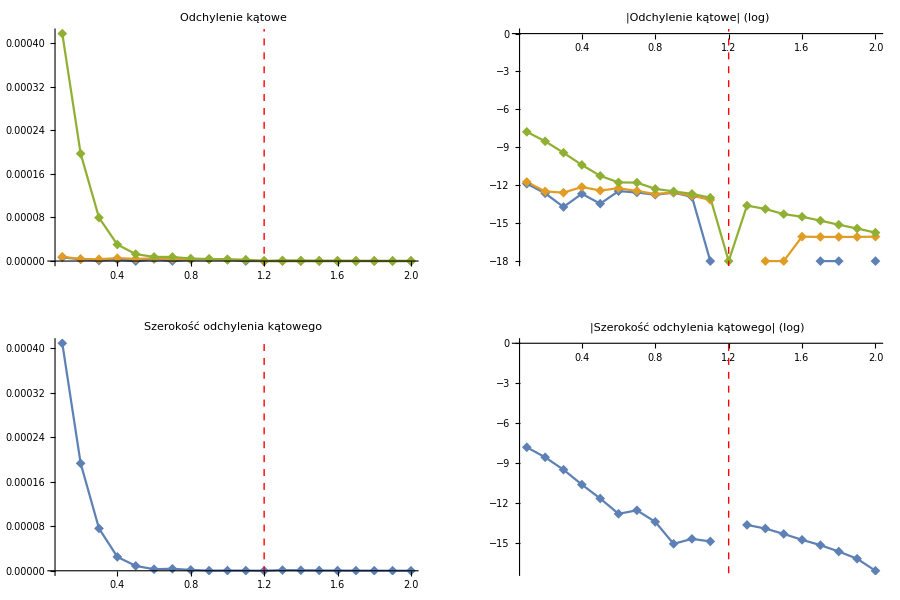

```mathematica
plotAngDev[1,2,1,3]
plotAngDevWidth
GraphicsGrid[{{angDevPlot,angDevLogPLot},{angDevWidthPlot,angDevWidthLogPlot}},Frame->All,ImageSize->900,AspectRatio->1/1.5]
```

### Coefficients a1, a2, a3

#### Normalised a2 (a2/a1^2) and log scale

```mathematica
plota2Normalised[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
a2Normalised = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, a2Column]][[All,stepMin;;stepMax]]]/Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2,a1Column]][[All,stepMin;;stepMax]]]^2,q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];
(*LOG SCALE*)
a2NormalisedLog = Table[{etaRange[[i]], Log@Quantile[Abs@(Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, a2Column]][[All,stepMin;;stepMax]]]/Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2,a1Column]][[All,stepMin;;stepMax]]]^2),q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];
(*PLOTS*)
a2NormalisedPlot=ListLinePlot[a2Normalised,PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Wartość a2/a1^2",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
a2NormalisedLogPLot=ListLinePlot[a2NormalisedLog, PlotRange->All,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"|Wartość a2/a1^2| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];]
```

#### Width of normalised a2

```mathematica
plota2NormalisedWidth:=Module[{},
a2NormalisedWidth=a2Normalised[[2]];
a2NormalisedWidth[[All,2]]=a2Normalised[[3,All,2]]-a2Normalised[[1,All,2]];
a2NormalisedWidthPlot=ListLinePlot[{a2NormalisedWidth},(*PlotLegends->Placed[{"Width of length deviation"},{0.35,0.75}],*)PlotRange->All,PlotLabel->"Szerokość rozkładu a2/a1^2",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
(*Width of normalised a2 in logarithmic scale*)
a2NormalisedWidthLog=a2NormalisedWidth;
a2NormalisedWidthLog[[All,2]]=Log@Abs@a2NormalisedWidth[[All,2]];
a2NormalisedWidthLogPlot=ListLinePlot[{a2NormalisedWidthLog}(*,PlotLegends->Placed[{"Width of normalised a2"},{0.35,0.75}]*),PlotRange->All,PlotLabel->"|Szerokość rozkładu a2/a1^2| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### a2 Normalised: final results

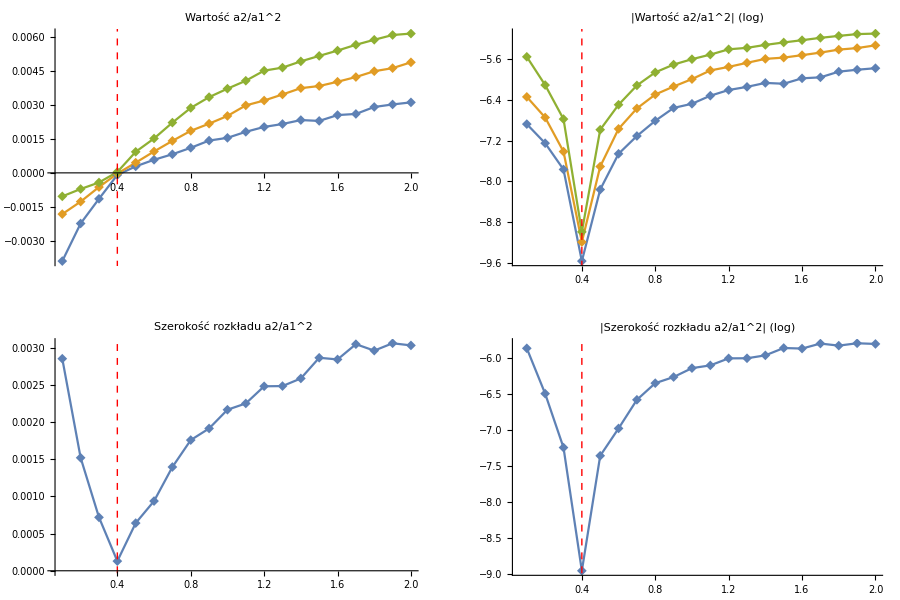

```mathematica
plota2Normalised[1,2,1,25]
plota2NormalisedWidth
GraphicsGrid[{{a2NormalisedPlot,a2NormalisedLogPLot},{a2NormalisedWidthPlot,a2NormalisedWidthLogPlot}},AspectRatio->1/1.5,Frame->All,ImageSize->900]
```

### River graph

```mathematica
plotSimData[data_, color_:Black]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,data["Model", "width"]},{0,5.75}},
(*PlotRange->{{0,data["Model", "width"]},{0,data["Model", "height"]}},*) 
PlotLabel -> "Początkowa sieć rzeczna",
 ImageSize -> 400,
AspectRatio->1/1.5,
PlotRangePadding->0,

PlotStyle->color];
```

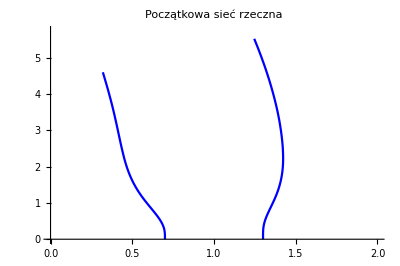

```mathematica
plotSimData[ImportJSONData[folder<>"/original_eta.json"]]
```

```mathematica
plotRiver:=Module[{},
riverPlot = plotSimData[ImportJSONData[folder<>"/original_eta.json"]];
]
```

### Final results

```mathematica
replotFinal[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
plotGeoDev[streamMin,streamMax,stepMin,stepMax];
plotGeoDevWidth;
plotAngDev[streamMin,streamMax,stepMin,stepMax];
plotAngDevWidth;
plota2Normalised[streamMin,streamMax,stepMin,stepMax];
plota2NormalisedWidth;
plotRiver;
final=GraphicsGrid[{{riverPlot,geoDevLogPLot,geoDevWidthLogPlot},{angDevPlot,angDevLogPLot,angDevWidthLogPlot},{a2NormalisedPlot,a2NormalisedLogPLot,a2NormalisedWidthLogPlot}},ImageSize->1100,AspectRatio->1/1.5]
]

plotFinal:=Module[{},
final=GraphicsGrid[{{riverPlot,geoDevLogPLot,geoDevWidthLogPlot},{angDevPlot,angDevLogPLot,angDevWidthLogPlot},{a2NormalisedPlot,a2NormalisedLogPLot,a2NormalisedWidthLogPlot}},ImageSize->1100,AspectRatio->1/1.5]
]
```

### Simplified final

```mathematica
replotSimpFinal[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
plotGeoDev[streamMin,streamMax,stepMin,stepMax];
plotAngDev[streamMin,streamMax,stepMin,stepMax];
plota2Normalised[streamMin,streamMax,stepMin,stepMax];
simpFinal=GraphicsRow[{geoDevLogPLot,angDevPlot,a2NormalisedPlot},ImageSize->1100,AspectRatio->1/1.5]
]

plotSimpFinal:=Module[{},
simpFinal=GraphicsRow[{geoDevLogPLot,angDevPlot,a2NormalisedPlot},ImageSize->1100,AspectRatio->1/1.5]
]
```

## Setting initial parameters

## Results

```mathematica
(*initialization[etaOrigin_, etaMin_,etaMax_,fName_:"/back_lap"]*)
initialization[4,1,20]
(*replotFinal[streamMin_,streamMax_,stepMin_,stepMax_]*)
replotFinal[1,2,1,25]
```

```mathematica
Do[
initialization[i,1,20];
Export["lap"<>ToString[i]<>".pdf",replotFinal[1,2,0,25]];
,{i, Range[1,1]}
]
```